# Chapter 9 - Problem 2

## Drawing of the Problem : -Graphics-

## Prerequisite Information:

Some information that we need before we go on. We will need to solve the differential equation given in the notes, and then find the derivatives. Similar to chapter 8, except this time our partial differential equation is different than before. (n is the order of the Bessel function NOT the energy level)

```mathematica
D[BesselJ[n,kr*r],r]
D[BesselY[n,kr*r],r]
D[BesselJ[n,kr*r] + BesselY[n,kr*r],r ] 
D[HankelH1[n,kr*r],r]
```

1/2 kr (BesselJ[-1+n,kr r]-BesselJ[1+n,kr r])

1/2 kr (BesselY[-1+n,kr r]-BesselY[1+n,kr r])

1/2 kr (BesselJ[-1+n,kr r]-BesselJ[1+n,kr r])+1/2 kr (BesselY[-1+n,kr r]-BesselY[1+n,kr r])

1/2 kr (HankelH1[-1+n,kr r]-HankelH1[1+n,kr r])

## Part I. Constants, Conversion Factors and Given Information.

```mathematica
ClearAll["Global`*"];
h = 6.62607004 * 10^-34; (* Plankton's Constant *)
mo = 9.10938 * 10^-31; (* Effective mass of an electron *)
ℏ = h/(2*π);
nano = 1*10^-9;
e = 1.60217 * 10^-19;
Vo = -0.5 ; (*potential in the wire*)
Vc = 0 ; (* potential in cladding*) 
r0 = 2 * nano ;(* Radius of the wire *)
```

## Part II. K’s and Derivative of the Bessel Functions

```mathematica
kwire=√((2*mo*e*(En-Vo))/ℏ^2);
kclad= √(-(2*mo*e*En)/ℏ^2);
BesselKPrime[M_,r_] = D[BesselK[M,r],r];
BesselJPrime[M_,r_] = D[BesselJ[M,r],r];
```

## Part III. Calculating the determinant and the roots

In Chapter 8, we used the boundary conditions to get the determinant of the wave equation since we know that a wave equation and it’s derivative must equal to 0. (Continuity conditions discussed in chapter 8). We’re going to do the same thing here.

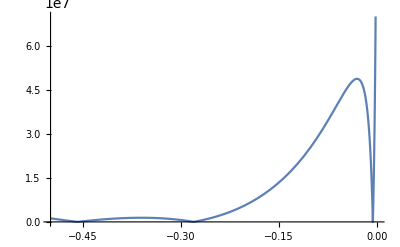

```mathematica
Clear[n]
n = 0; (* order of the Bessel functions AND energy state desired *)
determinant = BesselJ[n,kwire*r0]*kclad*BesselKPrime[n, kclad*r0]- BesselK[n, kclad*r0]*kwire*BesselJPrime[n, kwire*r0];
Plot[Abs[determinant],{En, -.499, -0.00001}]
```

## Lowest Energy States are the roots

You can change the n value to compute more than just ground state. First example when n = 1, you can plot for the first excited state, n = 2 is the second excited state, etc.

```mathematica
FindRoot[Abs[determinant],{En,-0.499}]
FindRoot[Abs[determinant],{En,-0.3}]
FindRoot[Abs[determinant],{En,-0.000001}]
```

{En→-0.457625}

{En→-0.280909}

{En→-0.00703041}

# Mannasah’s Method

Professor Mannasah decides to use Hankel Functions (which is a linear combination of BesselJ and BesselY)
Link to a little more information of the Hankel Function: http://mathworld.wolfram.com/HankelFunctionoftheFirstKind.html

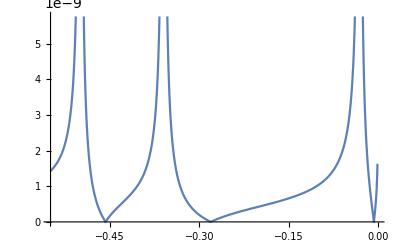

{een→-0.00703041+0. ⅈ}

{een→-0.457625+0. ⅈ}

{een→-0.280909+0. ⅈ}

```mathematica
Clear["Global`*"];

aa=(I* √2*√m*√(-een*e+v0))/hb;
bb=(√2*√(een*e)*√m)/hb;

h=6.62607004*10^(-34);
hb=h/(2*Pi);
m=9.10938*10^(-31);
e=1.60217*10^(-19);
v0=e*(-0.5);
r0=2*(10^(-9));

Plot[Abs[BesselJ[0,aa*r0]/(-aa*BesselJ[1,aa*r0])-HankelH1[0,bb*r0]/(-bb*HankelH1[1,bb*r0])],{een,-0.55,-0.001}]

FindRoot[BesselJ[0,aa*r0]/(-aa*BesselJ[1,aa*r0])==HankelH1[0,bb*r0]/(-bb*HankelH1[1,bb*r0]),{een,-0.01}]

FindRoot[BesselJ[0,aa*r0]/(-aa*BesselJ[1,aa*r0])==HankelH1[0,bb*r0]/(-bb*HankelH1[1,bb*r0]),{een,-0.38}]

FindRoot[BesselJ[0,aa*r0]/(-aa*BesselJ[1,aa*r0])==HankelH1[0,bb*r0]/(-bb*HankelH1[1,bb*r0]),{een,-0.08}]
```